## out of plane

### useful function

```mathematica
Load Last Line Energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Load Energy[type_,D_,χ_,xbegin_,xend_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_chi",#4,"_tol1.0e-10_maxiter10_miniter1.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,xbegin,xend,0.01}];

data=Load Last Line Energy/@files;
Transpose[{Table[i,{i,xbegin,xend,0.01}],data}])
Load Energy2[type_,D_,χ_,xbegin_,xend_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_chi",#4,"_tol1.0e-10_maxiter10_miniter2.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,xbegin,xend,0.01}];

data=Load Last Line Energy/@files;
Transpose[{Table[i,{i,xbegin,xend,0.01}],data}])
```

### K-J-Γ-Γ’

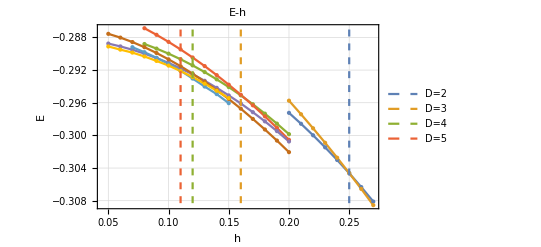

```mathematica
data={Load Energy[zigzag,2,20,0.20,0.27],Load Energy[ferro,2,20,0.20,0.27],Load Energy[zigzag,3,20,0.08,0.20],Load Energy[ferro,3,20,0.08,0.20],Load Energy2[zigzag,4,80,0.05,0.20],Load Energy2[random,4,80,0.05,0.20],Load Energy[ferro,5,100,0.07,0.15],Load Energy[zigzag,5,100,0.05,0.15]};
cirtical line={{{0.25,-1},{0.25,0}},{{0.16,-1},{0.16,0}},{{0.12,-1},{0.12,0}},{{0.11,-1},{0.11,0}}};

Show[ListPlot[data,Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]},PlotStyle->PointSize[Medium]],
ListPlot[cirtical line,PlotLegends->{"D=2","D=3","D=4","D=5"},Joined->True,Mesh->All,PlotStyle->Dashed,PlotRange->{{0.05,0.27},{-0.31,-0.285}}]]
```

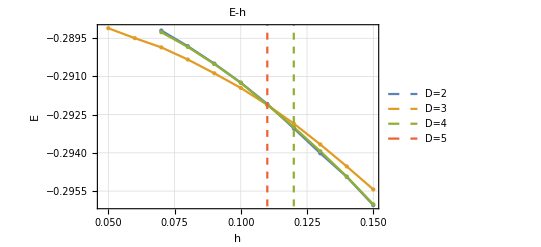

```mathematica
data={Load Energy[ferro,5,100,0.07,0.15],Load Energy[zigzag,5,100,0.05,0.15],Load Energy[random,5,100,0.07,0.15]};
cirtical line={{{0.25,-1},{0.25,0}},{{0.16,-1},{0.16,0}},{{0.12,-1},{0.12,0}},{{0.11,-1},{0.11,0}}};

Show[ListPlot[data,Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]},PlotStyle->PointSize[Medium]],
ListPlot[cirtical line,PlotLegends->{"D=2","D=3","D=4","D=5"},Joined->True,Mesh->All,PlotStyle->Dashed,PlotRange->{{0.05,0.27},{-0.31,-0.285}}]]
```

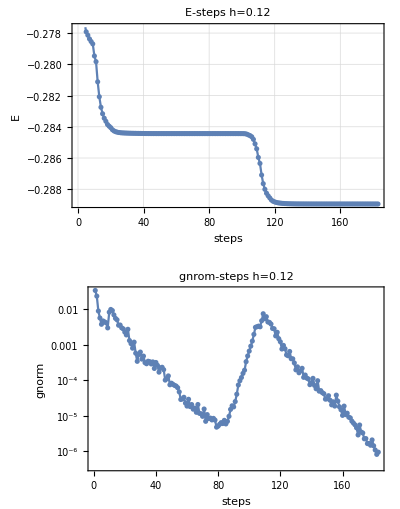

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_0.12_ferro\\D2_chi20_tol1.0e-10_maxiter10_miniter1.log"];GraphicsGrid[{{ListPlot[Table[{i,data[[4(i-1)+3]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps h=0.12"],LabelStyle->{GrayLevel[0]}]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps h=0.12"]]}}]
```

## in plane

### useful function

```mathematica
Load Last Line Energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Load Energy[type_,D_,χ_,xbegin_,xend_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_",#1,"_",#2,"\\D",#3,"_chi",#4,"_tol1.0e-10_maxiter10_miniter1.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,xbegin,xend,0.01}];

data=Load Last Line Energy/@files;
Transpose[{Table[i,{i,xbegin,xend,0.01}],data}])
Load Energy2[type_,D_,χ_,xbegin_,xend_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_",#1,"_",#2,"\\D",#3,"_chi",#4,"_tol1.0e-10_maxiter10_miniter2.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,xbegin,xend,0.01}];

data=Load Last Line Energy/@files;
Transpose[{Table[i,{i,xbegin,xend,0.01}],data}])
```

### K-J-Γ-Γ’

#### D=4

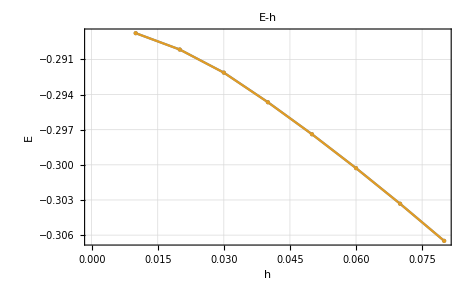

```mathematica
data={Load Energy[zigzag,4,80,0.01,0.08],Load Energy[ferro,4,80,0.01,0.08]};
cirtical line={{{0.25,-1},{0.25,0}},{{0.16,-1},{0.16,0}},{{0.12,-1},{0.12,0}},{{0.11,-1},{0.11,0}}};

Show[ListPlot[data,Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]},PlotStyle->PointSize[Medium]],
ListPlot[cirtical line,PlotLegends->{},Joined->True,Mesh->All,PlotStyle->Dashed,PlotRange->All]]
```

```mathematica
data
```

{{{0.01,-0.288756},{0.02,-0.290153},{0.03,-0.292124},{0.04,-0.29465},{0.05,-0.297383},{0.06,-0.300278},{0.07,-0.30332},{0.08,-0.30649}},{{0.01,-0.288758},{0.02,-0.290156},{0.03,-0.292131},{0.04,-0.294656},{0.05,-0.297387},{0.06,-0.300283},{0.07,-0.303323},{0.08,-0.306494}}}

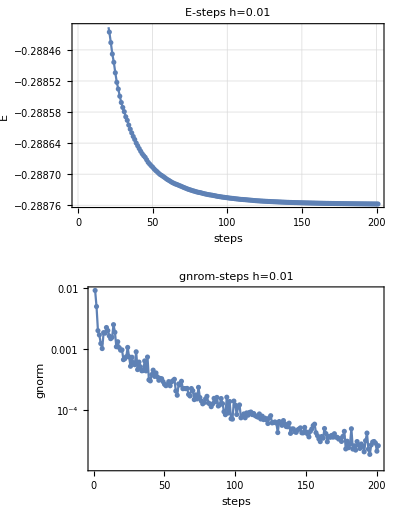

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_0.01_ferro\\D4_chi80_tol1.0e-10_maxiter10_miniter1.log"];GraphicsGrid[{{ListPlot[Table[{i,data[[4(i-1)+3]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps h=0.01"],LabelStyle->{GrayLevel[0]}]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps h=0.01"]]}}]
```

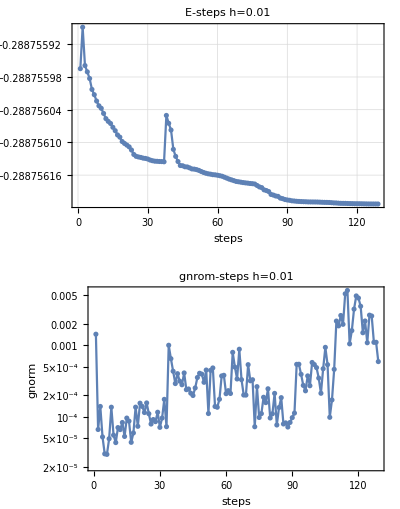

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_0.01_zigzag\\D4_chi80_tol1.0e-10_maxiter10_miniter1.log"];GraphicsGrid[{{ListPlot[Table[{i,data[[4(i-1)+3]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps h=0.01"],LabelStyle->{GrayLevel[0]}]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps h=0.01"]]}}]
```

#### D=5

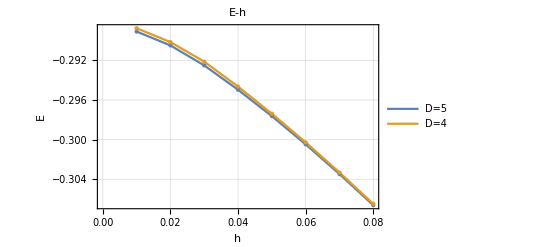

```mathematica
data={Load Energy[random,5,100,0.01,0.08],Load Energy[random,4,80,0.01,0.08]};
cirtical line={{{0.25,-1},{0.25,0}},{{0.16,-1},{0.16,0}},{{0.12,-1},{0.12,0}},{{0.11,-1},{0.11,0}}};

Show[ListPlot[data,Joined->True,Mesh->All,PlotTheme->"Detailed",PlotLegends->{"D=5","D=4"},FrameLabel->{{HoldForm["E"],None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]},PlotStyle->PointSize[Medium]],
ListPlot[cirtical line,PlotLegends->{},Joined->True,Mesh->All,PlotStyle->Dashed,PlotRange->All]]
```

```mathematica
data
```

{{{0.01,-0.288756},{0.02,-0.290153},{0.03,-0.292124},{0.04,-0.29465},{0.05,-0.297383},{0.06,-0.300278},{0.07,-0.30332},{0.08,-0.30649}},{{0.01,-0.288758},{0.02,-0.290156},{0.03,-0.292131},{0.04,-0.294656},{0.05,-0.297387},{0.06,-0.300283},{0.07,-0.303323},{0.08,-0.306494}}}

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_0.01_ferro\\D4_chi80_tol1.0e-10_maxiter10_miniter1.log"];GraphicsGrid[{{ListPlot[Table[{i,data[[4(i-1)+3]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps h=0.01"],LabelStyle->{GrayLevel[0]}]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps h=0.01"]]}}]
```

-Graphics-

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.9 - AutoDiff\\data\\AD_Kitaev\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, -2.0]_0.01_zigzag\\D4_chi80_tol1.0e-10_maxiter10_miniter1.log"];GraphicsGrid[{{ListPlot[Table[{i,data[[4(i-1)+3]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["E"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps h=0.01"],LabelStyle->{GrayLevel[0]}]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps h=0.01"]]}}]
```

-Graphics-